## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
```

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

These values taken from SM3 “predictions”

```mathematica
(** Current to field magnitude conversion factors for Bias **)
BxCalib=40.625;(*[G/A]*)
ByCalib=14.286;(*[G/A]*)
BzCalib=-10.368;(*[G/A]*)

(** Max current values **)
(* Chip *)
IlbMax=3.5; (* [A] *)
IzbMax=-3.5;(* [A] *)
IhMax=5.;(* [A] *)

(* Bias coils *)
IbxMax=8.;(*[A]*)
IbyMax=3.02;(*[A]*)
IbzMax=3.;(*[A]*)

(** Table values **)
(* These were taken from CAL3A_chiptrap_v1.pdf *)
(* Initial trap *)
tableZLHb={
(* Chip *)
AZ1=0.243,(* % *)
AZ2=-0.686,(* % *)
H1pH2=0.46,(* % *) 

(* Bias coils *)
T1=0.0275,(*%*)
T2=T1,
Y=0.85,(*%*)
Z=-0.05(*%*)
};

fdec=0.2;
tableZLHbDecomp={
(* Chip *)
tableZLHb⟦1⟧, (* AZ1 [%] *)
tableZLHb⟦2⟧,(* AZ2 [%] *)
tableZLHb⟦3⟧,(* H1pH2 [%] *)

(* Bias coils *)
fdec*tableZLHb⟦4⟧,(* T1 [%] *)
fdec*tableZLHb⟦5⟧,(* T2 [%] *)
fdec*tableZLHb⟦6⟧,(* Y [%] *)
fdec*tableZLHb⟦7⟧(* Z [%] *)
};

tableZHb={
(* Chip *)
0., (* AZ1 [%] *)
-0.743, (* AZ2 [%] *)
0.46, (* H1pH2 [%] *)

(* Bias coils *)
-0.018, (* T1 [%] *)
-0.018, (* T2 [%] *)
0.63,(* Y [%] *)
-0.0001 (* Z [%] *)
};

tableZHbC={
(* Chip *)
0., (* AZ1 [%] *)
0.914, (* AZ2 [%] *)
0.26, (* H1pH2 [%] *)

(* Bias coils *)
-0.006125,(* T1 [%] *)
-0.006125,(* T2 [%] *)
0.0677, (* Y [%] *)
-0.11367 (* Z [%] *)
};

(* Trap CurrL, CurrZ, CurrH, Bx1, By1, Bz1 *)
defineTableFromTrap[trap_]:=Module[
{CurrL=trap⟦1⟧,
CurrZ=trap⟦2⟧,
CurrH=trap⟦3⟧,
Bx1=trap⟦4⟧,
By1=trap⟦5⟧,
Bz1=trap⟦6⟧,
table},

table={
CurrL/IlbMax, (*AZ1 [%]*)
CurrZ/IzbMax, (*AZ2 [%]*)
CurrH/IhMax, (*H1pH2 [%]*)

Bx1/(-1.*IbxMax*BxCalib), (*T1*)
Bx1/(-1.*IbxMax*BxCalib), (*T2*)
By1/(IbyMax*ByCalib), (*Y*)
Bz1/(IbzMax*BzCalib) (*Z*)
};
Return[table];
];

defineTrapFromTable[table_]:=Module[
{AZ1=table⟦1⟧,
AZ2=table⟦2⟧,
H1pH2=table⟦3⟧,
T1=table⟦4⟧,
T2=table⟦5⟧, (* Currently T2=T1, and so doesn't play role yet *)
Y=table⟦6⟧,
Z=table⟦7⟧,
trap},

trap={
(* Chip *)
AZ1*IlbMax,(*Ilb0 [A]*)
AZ2*IzbMax,(*Izb0 [A]*)
H1pH2*IhMax,(*Ih0 [A]*)

(* Bias coils *)
(-1.)*T1*IbxMax*BxCalib,(*Bx [G]*)
Y*IbyMax*ByCalib,(*By [G]*)
Z*IbzMax *BzCalib(*Bz [G]*)
};
Return[trap];
]

(* The Bates trap *)
currLa=0;
currZa=0;
currLb=0;
currZb=2.6;
currH = 2.6;

Bx1 = (-0.048)*40.625;
By1 = (0.43)*14.286;
Bz1 = (0.3003)*(-10.3675);

trapZHbB={currLa,currZa,currLb,currZb,currH,Bx1,By1,Bz1};
tableZHbB=convertTrapParametersToCALTable[trapZHbB,verbose->True];
(* *)

(* Package for resale: *)
(* Compare these values to those in SM3 "predictions", although Bzfinal, for us, should be multiplied by 0.2 *)
trapzero=defineTrapFromTable[tableZLHb]
trapone=trapZHbB⟦3;;⟧
(*trapone=defineTrapFromTable@defineTableFromTrap@{CurrL,CurrZ,CurrH,Bx1,By1,Bz1}*)
```

AZ1_sel | AZ2_sel | AZ1 | AZ2 | H1&H2 | T1 | T2 | Y | Z
0 | 0 | 0. | -0.742857 | 0.52 | 0.006 | 0.006 | 0.142384 | 0.100095

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0,2.6,2.6,-1.95,6.14298,-3.11336}

### Define target ramp analytic function

```mathematica
cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
cassShort[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2(t/2)^(1/4) -1)]/Tanh[5];
```

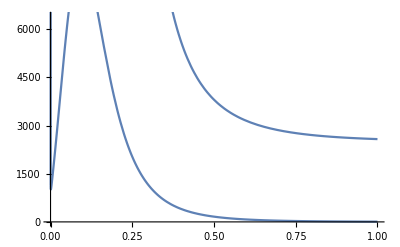

```mathematica
omegaPlot=Plot[cassShort[800,50,t]^2,{t,0,1},PlotRange->All];
dOmegaPlot=Plot[Evaluate[(1/0.5)*Abs@D[cassShort[800,50,t],t]],{t,0,1},PlotRange->All,PlotStyle->{"Red"}];
Show[omegaPlot,dOmegaPlot,PlotRange->{{0,1},{0,6400}}]
```

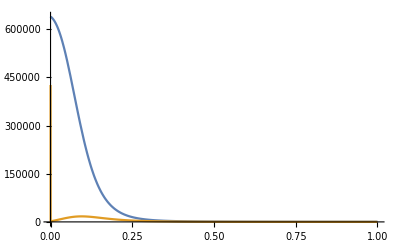

```mathematica
periodT=0.250 (* [s] *);
omegaI=800 (* [Hz] *);
omegaF=20 (* [Hz] *);
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->All,PlotStyle->{"Blue","Red"}]
```

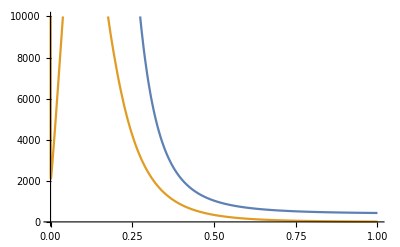

```mathematica
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->{{0,1},{0,1*10^4}},PlotStyle->{"Blue","Red"}]
```

21

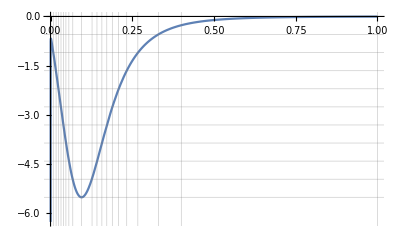

```mathematica
num=20;
times={0,0.0085,0.017,0.024,0.032,0.04,0.047,0.056,0.068,0.095,0.127,0.142,0.157,0.172,0.189,0.208,0.233,0.267,0.33,0.4,1};
Length@times
Plot[Evaluate[D[cassShort[1,0,t],{t,1}]],{t,0,1},GridLines->{times,Table[-k*max/(num/2),{k,1,num/2}]}]
```

```mathematica
Length@Differences@times
```

20

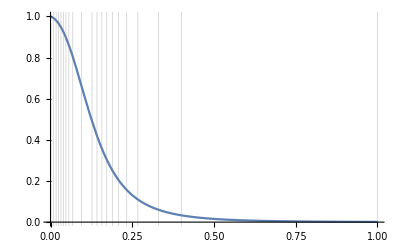

```mathematica
Plot[cassShort[1,0,t],{t,0,1},GridLines->{times,{}},PlotRange->Full]
```

```mathematica
max=MaxValue[{Abs@Evaluate[D[cassShort[1,0,t],{t,1}]],t>0.01},t]
```

5.51458

```mathematica
dCassShort[t_]=Evaluate[D[cassShort[1,0,t],{t,1}]];
```

```mathematica
(*InverseFunction@dCassShort*)
```

dCassShort^(-1)

```mathematica
(*cassShortInv=InverseFunction@dCassShort*)
```

```mathematica
(*cassShortInv[-max]*)
```

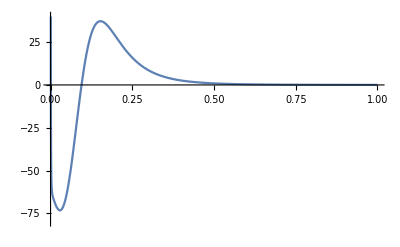

```mathematica
Plot[Evaluate[D[cassShort[1,0,t],{t,2}]],{t,0,1},PlotRange->{{0,1},{-80,40}}]
```

```mathematica
corgierSimp[t_]:=Module[{tau=2*Pi*t},
(1/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];
```

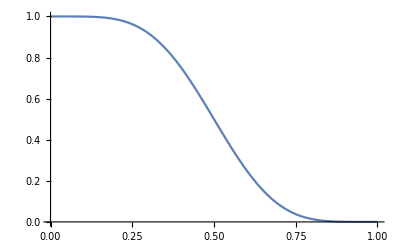

```mathematica
Plot[1-corgierSimp[t],{t,0,1}]
```

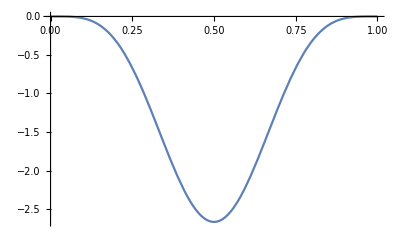

```mathematica
Plot[Evaluate@D[1-corgierSimp[t],t],{t,0,1}]
```

```mathematica
InverseFunction[corgierSimp][8/3]
```

Root2.56Root[{-32-(8 Sin[2 π #1])/π+Sin[4 π #1]/π+12 #1&,2.56420663113429131513147635321}]2.5642066311342915

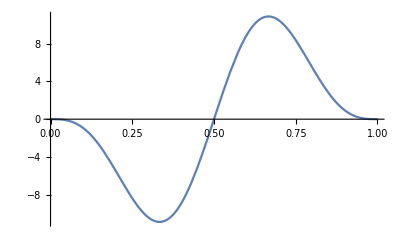

```mathematica
Plot[Evaluate@D[1-corgierSimp[t],{t,2}],{t,0,1}]
```

```mathematica
ArcCos[-1-2*Sqrt[2*6/10]]/(2*Pi)//N
```

0.5-0.290925 ⅈ

```mathematica
trapAnalytic[trap1_,trap2_,t_]:=trap1+(trap2-trap1)*(1-cassShort[1,0,t]);
zeroCrossing[trap1_,trap2_]:=(1/8)*((1/5)*ArcTanh[2*Tanh[5]*((1/2)-trap2[[6]]/(trap2[[6]]-trap1[[6]]))]+1)^4;
```

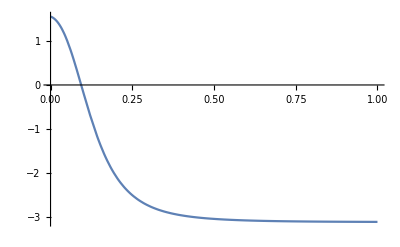

0.0937468

tZero = 0.0468734

```mathematica
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All]
tauZero=zeroCrossing[trapzero,trapone]
period=500*10^(-3);
deltaTau=10*^-3/period;
newTaus={tauZero-deltaTau,tauZero,tauZero+deltaTau};
Print["tZero = "<>ToString[tauZero*period]]
```

```mathematica
Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,rampin1sguess⟦1⟧}]
```

{{0.02,1.44003},{0.02,1.44003},{0.02,1.44003},{0.02,1.44003},{0.02,1.44003},{0.02,1.44003},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.05,1.02162},{0.08,0.350223},{0.14,-1.11223},{0.16,-1.49802},{0.18,-1.81564}}

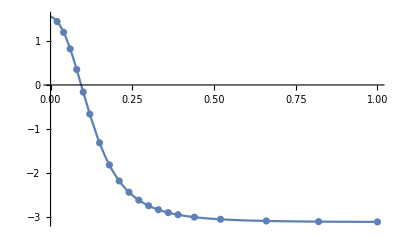

```mathematica
Show[{
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All],
ListPlot[Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,Accumulate@rampin1sguess⟦1⟧}]]
}]
```

### Define ramp ansatz

#### Trap 1 Short

```mathematica
rampin1sguess={{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
(*(* New as of 4 September 2020---an attempt to divy up the ramp based on its slope *)
Total@Differences@times
rampin1sguess={Differences@times,{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}*)
```

1.

{{0.0085,0.0085,0.007,0.008,0.008,0.007,0.009,0.012,0.027,0.032,0.015,0.015,0.015,0.017,0.019,0.025,0.034,0.063,0.07,0.6},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
Table[Total@#[[1,1;;m]],{m,Length@#[[1]]}]&[rampin1sguess]
```

{0.0085,0.017,0.024,0.032,0.04,0.047,0.056,0.068,0.095,0.127,0.142,0.157,0.172,0.189,0.208,0.233,0.267,0.33,0.4,1.}

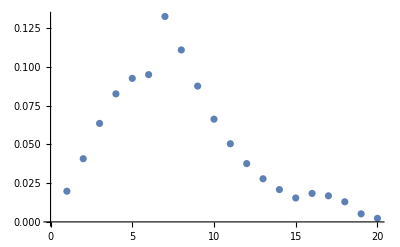

```mathematica
ListPlot[rampin1sguess⟦2⟧]
```

```mathematica
(*rampin1sguess⟦1,9;;13⟧
rampin1sguess⟦1⟧=Join[rampin1sguess⟦1,1;;9⟧,{0.01,0.01,0.01,0.01,0.01},rampin1sguess⟦1,10;;⟧]
rampin1sguess⟦1,9;;18⟧
rampin1sguess⟦1,9;;18⟧={0.02,0.02,0.02,0.01,0.01,0.01,0.01,0.01,0.02,0.02}*)
```

```mathematica
(*rampin1sguess⟦2,9;;13⟧
rampin1sguess⟦2⟧=Join[rampin1sguess⟦2,1;;9⟧,ConstantArray[0.,5],rampin1sguess⟦2,10;;⟧]*)
```

```mathematica
(*rampin1sguess*)
```

```mathematica
Total[rampin1sguess⟦1⟧]
```

1.

```mathematica
Total[rampin1sguess⟦2⟧]
```

1.

```mathematica
Length@rampin1sguess[[1]]
```

20

## Calculate ramp

```mathematica
nramps1short=Length@rampin1sguess⟦1⟧
```

20

The following took 8 1/2 minutes to complete. (1 1/4 hr on the Dell)

```mathematica
(* 
If FitCurveHacked runs in less than a second and has multiple errors citing GeometricMean, go back and make sure bubble-4a.nb was run before this notebook. MovingTrap-murphree.m calls ChipTrapFrequencies, which is defined in that notebook.
*)
```

```mathematica
(rampin1s=FitCurveHacked[trapzero,trapone,rampin1sguess,nramps1short,-3.5,-5])//Timing
```

{0.00744,-0.701104,0.00001}

Completed point 1 of 19 in 20.125 s (Total time: 0.335417 min).

{0.00778,1.00501,0.00001}

{0.00908,0.32206,0.00001}

{0.00973,-0.0194731,0.00001}

Completed point 2 of 19 in 34.6563 s (Total time: 0.913021 min).

{0.01239,-0.655014,0.00001}

{0.01136,-0.112681,0.00001}

Completed point 3 of 19 in 29.625 s (Total time: 1.40677 min).

{0.01656,-0.23412,0.00001}

{0.01518,0.494255,0.00001}

{0.01587,0.130086,0.00001}

Completed point 4 of 19 in 36.5 s (Total time: 2.0151 min).

{0.01929,0.558757,0.00001}

{0.02251,-1.14565,0.00001}

Completed point 5 of 19 in 32. s (Total time: 2.54844 min).

{0.02078,0.0127745,0.00001}

Completed point 6 of 19 in 19.4375 s (Total time: 2.8724 min).

{0.02902,0.6282,0.00001}

{0.03386,-1.94609,0.00001}

Completed point 7 of 19 in 34.375 s (Total time: 3.44531 min).

{0.05353,-4.12761,0.00001}

{0.04907,-1.75213,0.00001}

Completed point 8 of 19 in 34.2031 s (Total time: 4.01536 min).

{0.09563,11.5668,0.00001}

{0.11157,3.14621,0.00001}

{0.11954,-1.05526,0.00001}

{0.11755,-0.00679989,0.00001}

Completed point 9 of 19 in 34. s (Total time: 4.58203 min).

{0.41476,-122.695,0.00001}

{0.1359,3.2476,0.00001}

{0.14071,0.827766,0.00001}

{0.14311,-0.377445,0.00001}

{0.14251,-0.0762805,0.00001}

Completed point 10 of 19 in 52.7344 s (Total time: 5.46094 min).

{0.06573,-2.02429,0.00001}

{0.06026,0.61963,0.00001}

{0.063,-0.706011,0.00001}

Completed point 11 of 19 in 33.1875 s (Total time: 6.01406 min).

{0.05829,-0.689649,0.00001}

{0.05344,1.55512,0.00001}

{0.05586,0.43383,0.00001}

{0.05708,-0.130529,0.00001}

{0.05678,0.00819009,0.00001}

Completed point 12 of 19 in 45.25 s (Total time: 6.76823 min).

{0.05292,-0.496579,0.00001}

{0.04851,1.44125,0.00001}

{0.05072,0.468942,0.00001}

{0.05182,-0.0141172,0.00001}

Completed point 13 of 19 in 34.4375 s (Total time: 7.34219 min).

{0.04968,1.18338,0.00001}

{0.05796,-2.2133,0.00001}

{0.05278,-0.0928893,0.00001}

{0.05252,0.0139436,0.00001}

Completed point 14 of 19 in 42.8906 s (Total time: 8.05703 min).

{0.04734,1.6415,0.00001}

{0.05523,-1.35947,0.00001}

{0.05326,-0.613814,0.00001}

{0.05166,-0.00641974,0.00001}

Completed point 15 of 19 in 42.5625 s (Total time: 8.76641 min).

{0.05127,2.1621,0.00001}

{0.05981,-0.781815,0.00001}

{0.05768,-0.0519579,0.00001}

{0.05714,0.133541,0.00001}

{0.05741,0.0407679,0.00001}

{0.05754,-0.00388369,0.00001}

Completed point 16 of 19 in 59.0469 s (Total time: 9.75052 min).

{0.05214,3.01459,0.00001}

{0.06083,0.340732,0.00001}

{0.06517,-0.977392,0.00001}

Completed point 17 of 19 in 34.9688 s (Total time: 10.3333 min).

{0.12714,-12.5876,0.00001}

{0.07923,-0.708861,0.00001}

Completed point 18 of 19 in 34.8281 s (Total time: 10.9138 min).

{0.0422,1.18992,0.00001}

{0.04923,-0.487747,0.00001}

{0.04748,-0.0723489,0.00001}

{0.04704,0.0323265,0.00001}

{0.04726,-0.0200229,0.00001}

Completed point 19 of 19 in 45.9531 s (Total time: 11.6797 min).

{704.781,{{0.0085,0.0085,0.007,0.008,0.008,0.007,0.009,0.012,0.027,0.032,0.015,0.015,0.015,0.017,0.019,0.025,0.034,0.063,0.07,0.6},{0.0062,0.00973,0.01136,0.01587,0.0201,0.02078,0.03023,0.04572,0.11755,0.14251,0.06163,0.05678,0.05182,0.05252,0.05166,0.05754,0.06191,0.07647,0.04715,0.06247}}}

```mathematica
rampin1s⟦2⟧-rampin1sguess⟦2⟧
```

{-0.01362,-0.03105,-0.05221,-0.06678,-0.07254,-0.07428,-0.10238,-0.06528,0.02989,0.0762,0.0112,0.01915,0.02398,0.03166,0.03622,0.03915,0.04507,0.06349,0.04195,0.06018}

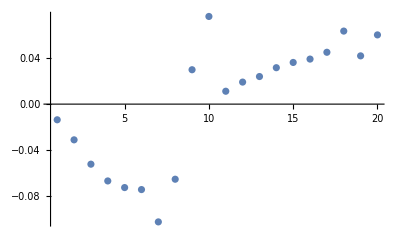

```mathematica
ListPlot[%,PlotRange->All]
```

The following took ~4 1/2 minutes to run. (~ 1 hr 12 min on Dell)

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzero,trapone,rampin1s,points1s,nramps1short];)//Timing
```

{332.766,Null}

### Plot calculated ramp’s parameters

{{0.,1.},{3.83329,6.83513}}

{46.2145,929.95}

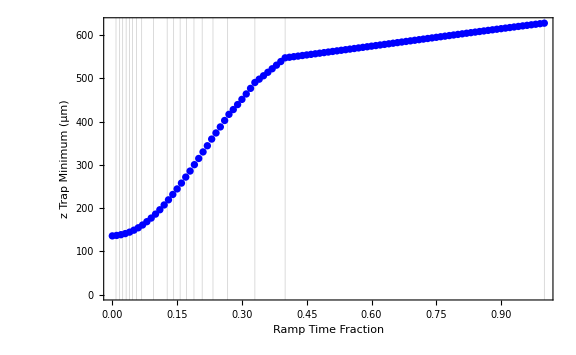
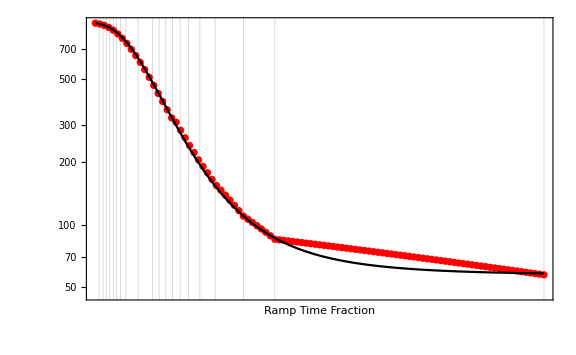

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

{{0.,1.},{2.99006,4.77009}}

{19.8868,117.929}

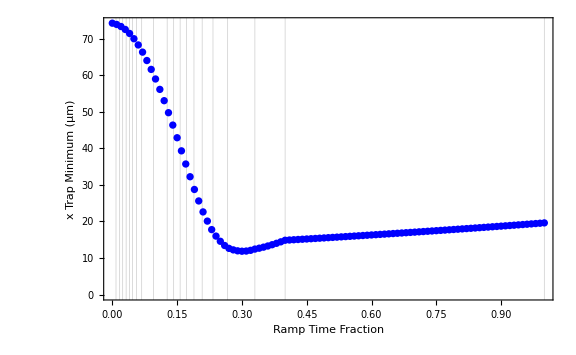
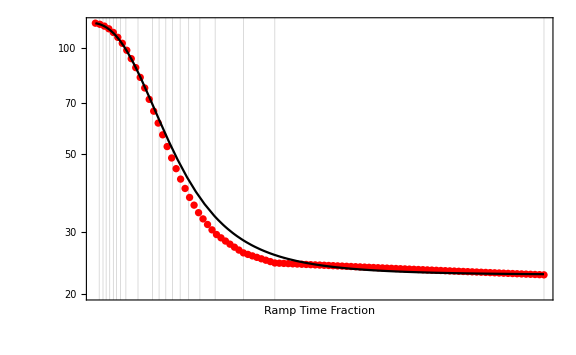

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

{{0.,1.},{3.77149,6.87598}}

{43.4445,968.724}

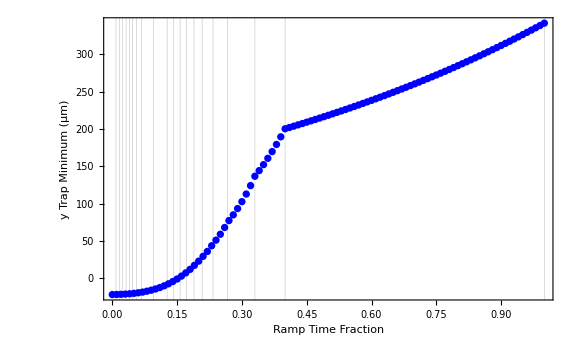
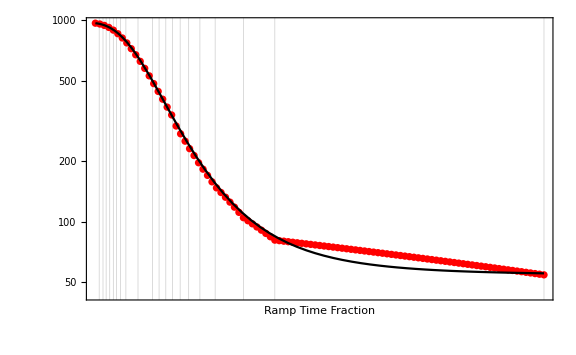

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

{{0.,1.},{3.83329,6.83513}}

{46.2145,929.95}

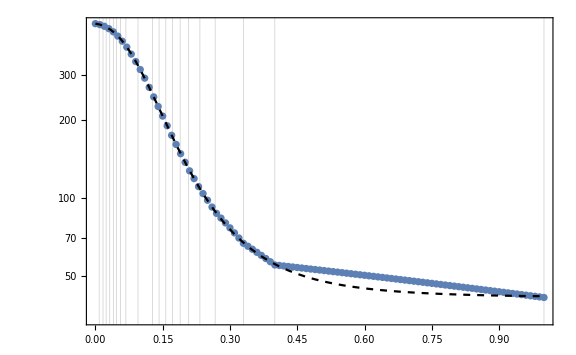

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

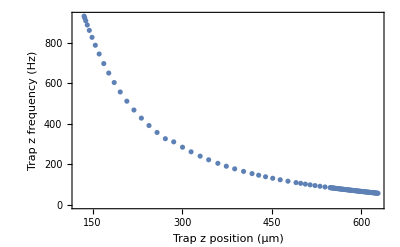

```mathematica
plotZFreqVZmin[movingtrap_]:=Module[{zs,omegas},
zs[n_]:=movingtrap⟦n,1,3⟧*10^6;
omegas[n_]:=movingtrap⟦n,2,3⟧;

ListPlot[Table[{zs[n],omegas[n]},{n,Range[Length[movingtrap]]}],Frame->True,FrameLabel->{"Trap z position (μm)","Trap z frequency (Hz)"}]
]
plotZFreqVZmin[pts1s]
```

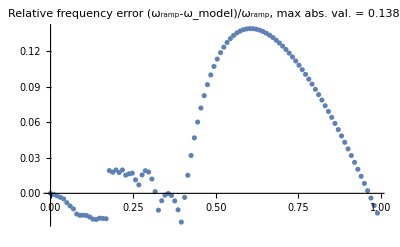

```mathematica
plotFreqError[pts1s]
```

```mathematica
printTrapParameters[{{minx_,miny_,minz_},{omegax_,omegay_,omegaz_},bmin_}]:=Print[
"Position = "<>ToString[{minx,miny,minz}*10^6]<>" μm\n"<>
"Frequency = "<>ToString[{omegax,omegay,omegaz}]<>" Hz\n"<>
"Bmin = "<>ToString[bmin]<>" G"];

printTrapParameters[pts1s⟦1⟧]
printTrapParameters[pts1s⟦-1⟧]
```

Position = {74.2507, -21.9915, 135.717} μm
Frequency = {117.929, 968.724, 929.95} Hz
Bmin = 8.97843 G

Position = {19.6048, 341.948, 627.837} μm
Frequency = {22.6293, 54.4236, 57.4638} Hz
Bmin = 4.98191 G

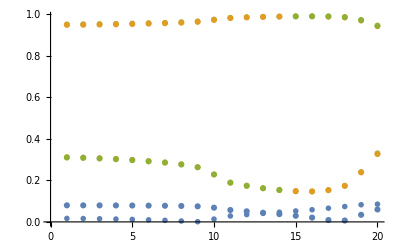

```mathematica
plotTrapPrincAxes[trap1_,trap2_,rampin_]:=Module[
{nramps=Length@rampin⟦1⟧,
eVecIndex,
characVtime,
vec2Plot,vec3Plot},
characVtime=Table[SingleTrapCharacteristics[trap1,trap2,rampin,nramps,n],{n,nramps}];
eVecIndex=2;
vec2Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}],PlotMarkers->"OpenMarkers"];
eVecIndex=3;
vec3Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}]];
Show[vec2Plot,vec3Plot]
]
plotTrapPrincAxes[trapzero,trapone,rampin1s]
```

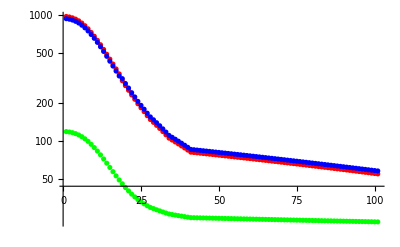

```mathematica
plotTrapYandZCharacteristics[movingramp_]:=Module[
{xFreqs=movingramp⟦All,2,1⟧,
yFreqs=movingramp⟦All,2,2⟧,
zFreqs=movingramp⟦All,2,3⟧,
xPlot,yPlot,zPlot},
xPlot=ListLogPlot[xFreqs,PlotStyle->Green];
yPlot=ListLogPlot[yFreqs,PlotStyle->Red];
zPlot=ListLogPlot[zFreqs,PlotStyle->Blue];
Show[yPlot,zPlot,xPlot,PlotRange->All]
]
plotTrapYandZCharacteristics[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

{{0.0085,0.0085,0.007,0.008,0.008,0.007,0.009,0.012,0.027,0.032,0.015,0.015,0.015,0.017,0.019,0.025,0.034,0.063,0.07,0.6},{0.0062,0.01593,0.02729,0.04316,0.06326,0.08404,0.11427,0.15999,0.27754,0.42005,0.48168,0.53846,0.59028,0.6428,0.69446,0.752,0.81391,0.89038,0.93753,1.}}

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

20200904T122408

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_trap1short.csv"},trap1shortᵀ]
```

C:\Users\josep\forschung\modeling\bubble_bec\output\20200904T122408_trap1short.csv

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

{{0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0,2.6,2.6,-1.95,6.14298,-3.11336}}

C:\Users\josep\forschung\modeling\bubble_bec\output\20200904T122408_ramp_endpoints.csv

```mathematica
Beep[];
Pause[1];
Beep[];
```

```mathematica
defineTableFromTrap[trapone]
```

{0.,-0.742857,0.52,0.006,0.006,0.142384,0.100095}

## Look at intermediate trap and CAL table values

{{0., 0.8505}, {0.01, 0.843767}, {0.02, 0.832811}, {0.03, 0.817167}, {0.04, 0.796697}, {0.05, 0.770454}, {0.06, 0.740352}, {0.07, 0.707023}, {0.08, 0.669995}, {0.09, 0.632966}, {0.1, 0.595514}, {0.11, 0.557638}, {0.12, 0.519761}, {0.13, 0.482764}, {0.14, 0.44782}, {0.15, 0.415076}, {0.16, 0.383725}, {0.17, 0.354343}, {0.18, 0.327447}, {0.19, 0.301486}, {0.2, 0.278361}, {0.21, 0.255947}, {0.22, 0.236372}, {0.23, 0.216797}, {0.24, 0.200083}, {0.25, 0.184597}, {0.26, 0.16911}, {0.27, 0.155173}, {0.28, 0.144849}, {0.29, 0.134526}, {0.3, 0.124202}, {0.31, 0.113879}, {0.32, 0.103555}, {0.33, 0.0932318}, {0.34, 0.0875031}, {0.35, 0.0817744}, {0.36, 0.0760456}, {0.37, 0.0703169}, {0.38, 0.0645882}, {0.39, 0.0588595}, {0.4, 0.0531307}, {0.41, 0.0522452}, {0.42, 0.0513597}, {0.43, 0.0504742}, {0.44, 0.0495887}, {0.45, 0.0487032}, {0.46, 0.0478177}, {0.47, 0.0469321}, {0.48, 0.0460466}, {0.49, 0.0451611}, {0.5, 0.0442756}, {0.51, 0.0433901}, {0.52, 0.0425046}, {0.53, 0.0416191}, {0.54, 0.0407336}, {0.55, 0.0398481}, {0.56, 0.0389625}, {0.57, 0.038077}, {0.58, 0.0371915}, {0.59, 0.036306}, {0.6, 0.0354205}, {0.61, 0.034535}, {0.62, 0.0336495}, {0.63, 0.032764}, {0.64, 0.0318784}, {0.65, 0.0309929}, {0.66, 0.0301074}, {0.67, 0.0292219}, {0.68, 0.0283364}, {0.69, 0.0274509}, {0.7, 0.0265654}, {0.71, 0.0256799}, {0.72, 0.0247943}, {0.73, 0.0239088}, {0.74, 0.0230233}, {0.75, 0.0221378}, {0.76, 0.0212523}, {0.77, 0.0203668}, {0.78, 0.0194813}, {0.79, 0.0185958}, {0.8, 0.0177102}, {0.81, 0.0168247}, {0.82, 0.0159392}, {0.83, 0.0150537}, {0.84, 0.0141682}, {0.85, 0.0132827}, {0.86, 0.0123972}, {0.87, 0.0115117}, {0.88, 0.0106261}, {0.89, 0.00974063}, {0.9, 0.00885512}, {0.91, 0.00796961}, {0.92, 0.0070841}, {0.93, 0.00619859}, {0.94, 0.00531307}, {0.95, 0.00442756}, {0.96, 0.00354205}, {0.97, 0.00265654}, {0.98, 0.00177102}, {0.99, 0.000885512}, {1., 0.}}

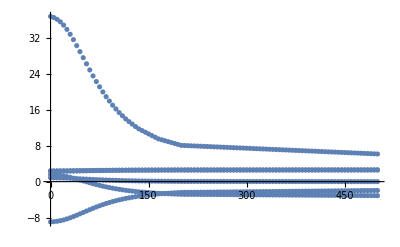

```mathematica
listRampCALTables[trap1_,trap2_,rampin_,npoints_,nramps_:3]:=Module[
{
deltatrap=trap1-trap2,
ramp=Prepend[Table[{Sum[#[[1,i]],{i,n}],Sum[#[[2,i]],{i,n}],#[[2,n]]/#[[1,n]]},{n,nramps}]&[rampin],{0,0,0}],
ramplist,
colors={"Red","Orange","Yellow","Green","Blue","Black"}
},

ramplist=Prepend[Drop[Table[{t,Piecewise[Table[{#3-(#1[[n-1,2]]+#1[[n,3]]*(t-#1[[n-1,1]]))*#2,#1[[n-1,1]]<t<=#1[[n,1]]},{n,2,nramps+1}]&[ramp,deltatrap,trap1]]},{t,0.,1.,1./npoints}],1],{0.,trap1}];

Print[ToString[{#[[1]],#[[2,1]]}&/@ramplist]];

Return[Table[ListPlot[{#⟦1⟧*500,#⟦2,k⟧}&/@ramplist,PlotStyle->colors⟦k⟧],{k,6}]];
];
test=listRampCALTables[trapzero,trapone,rampin1s,points1s,nramps1short];
Show[test,PlotRange->All]
```

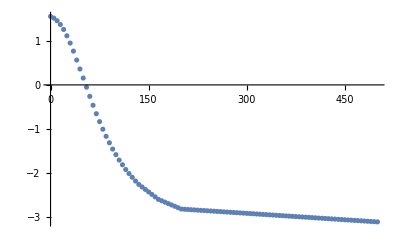

```mathematica
test[[6]]
```

```mathematica
rampin1s
```

{{0.0085,0.0085,0.007,0.008,0.008,0.007,0.009,0.012,0.027,0.032,0.015,0.015,0.015,0.017,0.019,0.025,0.034,0.063,0.07,0.6},{0.0062,0.00973,0.01136,0.01587,0.0201,0.02078,0.03023,0.04572,0.11755,0.14251,0.06163,0.05678,0.05182,0.05252,0.05166,0.05754,0.06191,0.07647,0.04715,0.06247}}

```mathematica
plotRampCALTable[trap1_,trap2_,rampin_]:=Module[
{
deltaTrap=trap2-trap1,
totRamp=Table[{Total@rampin⟦1,1;;k⟧,Total@rampin⟦2,1;;k⟧},{k,Length@rampin⟦1⟧}]~Prepend~{0,0},
trapRamp
},
trapRamp=Table[(totRamp⟦k,2⟧*deltaTrap+trap1)~Prepend~totRamp⟦k,1⟧,{k,Length@rampin⟦1⟧+1}];
Return[trapRamp];
];
trapRamp=plotRampCALTable[trapzero,trapone,rampin1s]
trapzero
trapone
```

{{0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.0085,0.845227,2.40223,2.30186,-8.89418,36.4829,1.52625},{0.017,0.836952,2.40417,2.30478,-8.82619,36.1858,1.48083},{0.024,0.82729,2.40643,2.30819,-8.74681,35.839,1.42779},{0.032,0.813792,2.40959,2.31295,-8.63592,35.3545,1.3537},{0.04,0.796697,2.41359,2.31898,-8.49547,34.7409,1.25987},{0.047,0.779024,2.41772,2.32521,-8.35027,34.1065,1.16285},{0.056,0.753313,2.42374,2.33428,-8.13904,33.1836,1.02172},{0.068,0.714429,2.43284,2.348,-7.81957,31.7878,0.808277},{0.095,0.614452,2.45623,2.38326,-6.99819,28.1991,0.259488},{0.127,0.493247,2.48459,2.42602,-6.0024,23.8484,-0.405829},{0.142,0.440831,2.49685,2.4445,-5.57176,21.9669,-0.693552},{0.157,0.39254,2.50815,2.46154,-5.17501,20.2334,-0.958633},{0.172,0.348467,2.51847,2.47708,-4.81292,18.6514,-1.20056},{0.189,0.303799,2.52892,2.49284,-4.44593,17.048,-1.44575},{0.208,0.259862,2.5392,2.50834,-4.08496,15.4709,-1.68693},{0.233,0.210924,2.55065,2.5256,-3.6829,13.7142,-1.95556},{0.267,0.15827,2.56297,2.54417,-3.2503,11.8242,-2.24459},{0.33,0.0932318,2.57819,2.56711,-2.71597,9.48959,-2.60159},{0.4,0.0531307,2.58757,2.58126,-2.38651,8.05014,-2.82172},{1.,0.,2.6,2.6,-1.95,6.14298,-3.11336}}

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0,2.6,2.6,-1.95,6.14298,-3.11336}

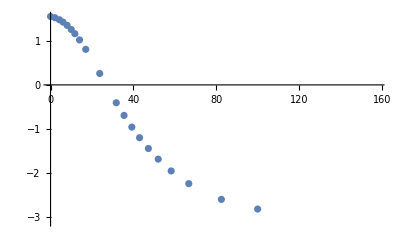

```mathematica
ListPlot[{#[[1]]*250,#[[7]]}&/@trapRamp]
```

```mathematica
Total@{1,2,3,4,5}
```

15